

```mathematica
(* 在图形中使用选项 *)
Plot[Sin[x],{x,0,2π}]
```

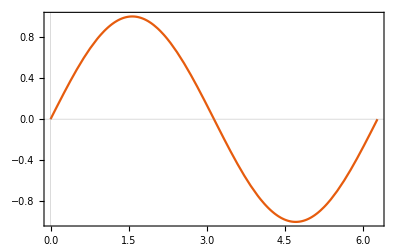

```mathematica
Plot[Sin[x],{x,0,2π},PlotTheme->"Scientific"] (* 使用科学计算绘图主题 *)
```

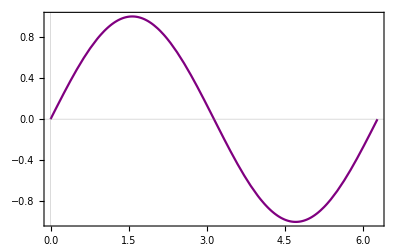

```mathematica
Plot[Sin[x],{x,0,2π},PlotTheme->"Scientific",PlotStyle->Purple]
```

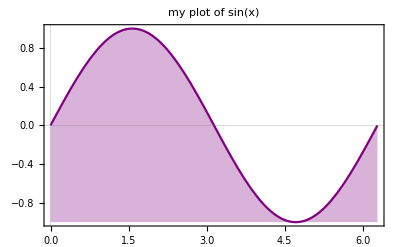

```mathematica
Plot[Sin[x],{x,0,2π},PlotTheme->"Scientific",PlotStyle->Purple,Filling->Bottom,PlotLabel->"my plot of sin(x)"]
```

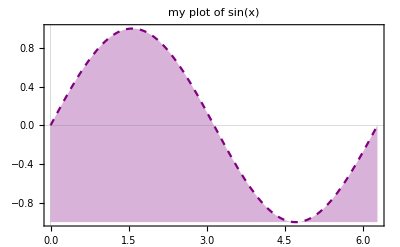

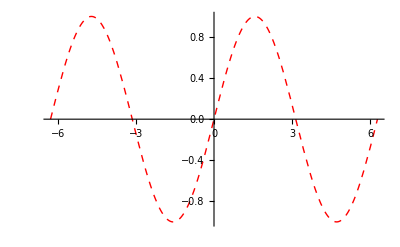

```mathematica
Plot[Sin[x],{x,0,2π},Filling->Bottom,PlotLabel->"my plot of sin(x)",PlotStyle->{Dashed,Purple},PlotTheme->"Scientific"] (* 如果有多个绘图样式，需要写在同一个列表中 *)
```

```mathematica
(* 使用建议栏进行样式交互式自定义 *)
Plot[Sin[x],{x,0,2π}]
```

-Graphics-

```mathematica
Plot[Sin[x],{x,0,2 π},PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
(* 使用绘图工具进行交互式自定义 双击图像 打开绘图工具 修改样式*)
Plot[Sin[x],{x,0,2π}]
```

-Graphics-

-Graphics-

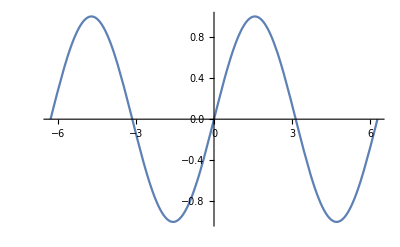

-Graphics-

```mathematica
Plot[Sin[x],{x,-2π,2π}]
```

```mathematica
(* 基于绘图工具对图形进行修改 *)
%
```

-Graphics-

-Graphics-

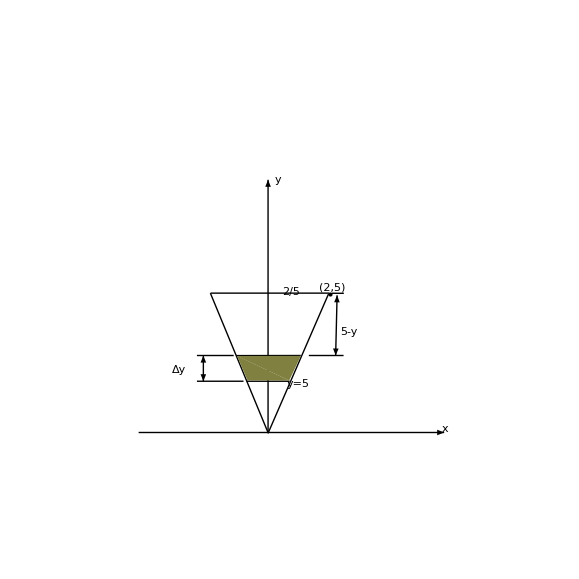
```mathematica
(* 使用绘图工具进行图形的绘制*)
-Graphics-
```

-Graphics-

```mathematica
(* 找出选项 *)
Take[Options[Plot], 10]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None}

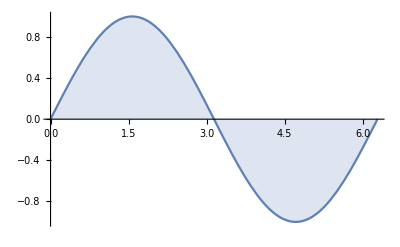

```mathematica
(* PlotTheme *)
Plot[Sin[x],{x,0,2π},Filling->Axis]
```

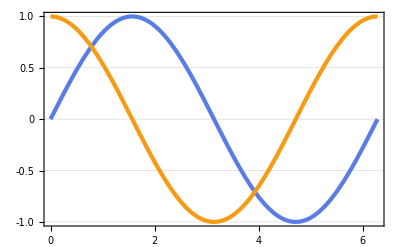

```mathematica
(* 自定义的一些常用选项 *)
GraphicsRow[{
	Plot[{Sin[x],Cos[x]},{x,0,2π},PlotTheme->"Business"],
	Plot3D[Sin[x y],{x,-2,2},{y,-2,2},PlotTheme->"Business"]
}]
```

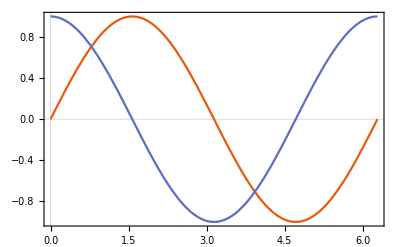

```mathematica
GraphicsRow[{
	Plot[{Sin[x],Cos[x]},{x,0,2π},PlotTheme->"Scientific"],
	Plot3D[Sin[x y],{x,-2,2},{y,-2,2},PlotTheme->"Scientific"]
}]
```

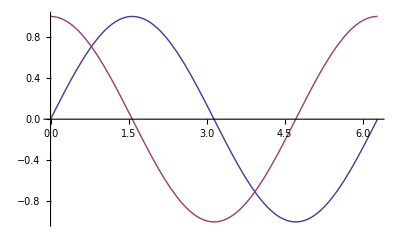

```mathematica
GraphicsRow[{
	Plot[{Sin[x],Cos[x]},{x,0,2π},PlotTheme->"Classic"],
	Plot3D[Sin[x y],{x,-2,2},{y,-2,2},PlotTheme->"Classic"]
}]
```

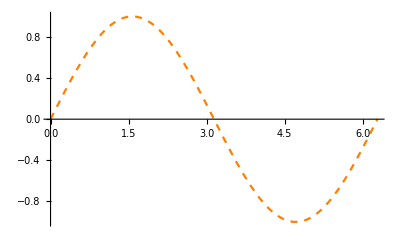

```mathematica
(* PlotStyle *)
Plot[Sin[x],{x,0,2π},PlotStyle->{Orange,Dashed}]
```

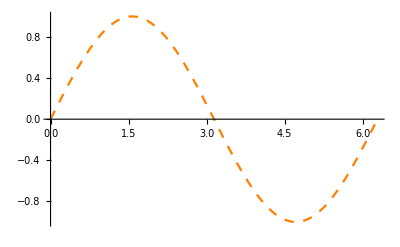

```mathematica
Plot[Sin[x],{x,0,2π},PlotStyle->{RGBColor[1,0.5,0],Dashing[{0.017,0.017}]}]
```

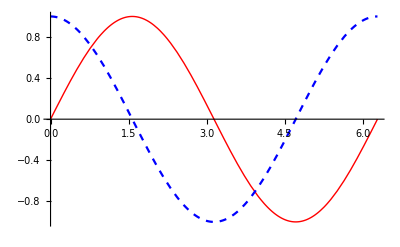

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2π},PlotStyle->{{Red,Thick},{Blue,Dashed}}]
```

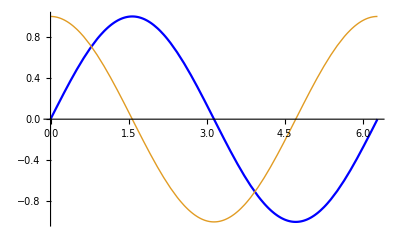

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2π},PlotStyle->{{Red,Blue},{Thick,Dash}}] (* 这是错误的写法 *)
```

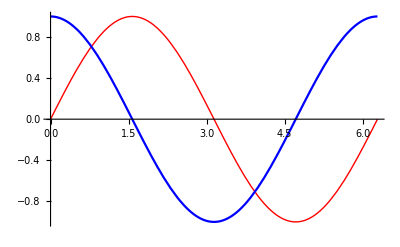

```mathematica
(* 基于Directive指令避免匹配时的麻烦 *)
Plot[{Sin[x],Cos[x]},{x,0,2π},PlotStyle->{Directive[Red,Thick],Directive[Blue,Thickness]}]
```

```mathematica
(* 着色函数 *)
Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction-> ColorData["Rainbow"]]
```

-Graphics3D-

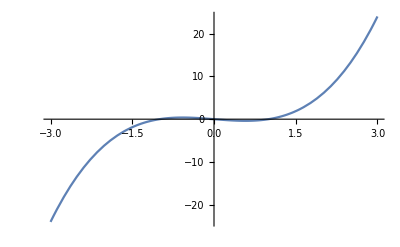

```mathematica
Plot[x^3-x,{x,-3,3}]
```

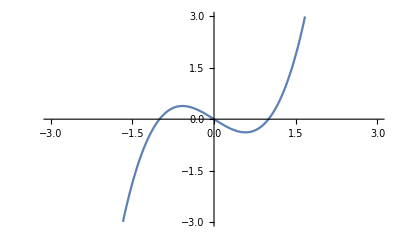

```mathematica
Plot[x^3-x,{x,-3,3},PlotRange->{-3,3}]
```

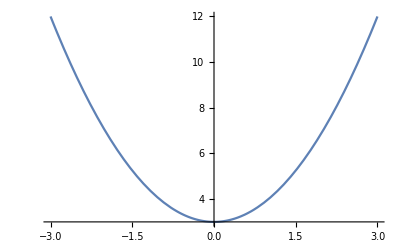

```mathematica
Plot[x^2+3,{x,-3,3}]
```

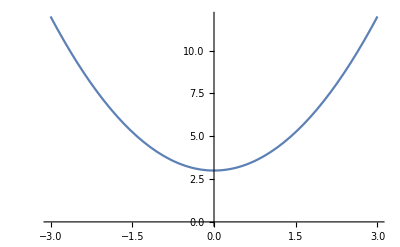

```mathematica
(* 强制坐标出现原点 *)
Plot[x^2+3,{x,-3,3},AxesOrigin->{0,0}]
```

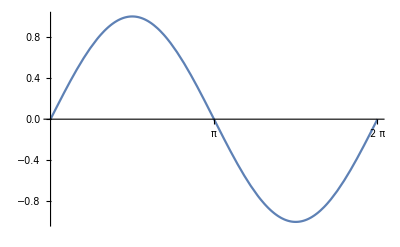

```mathematica
(* Thick *)
Plot[Sin[x],{x,0,2π},Ticks->{{1π, 2π}, Automatic}]
```

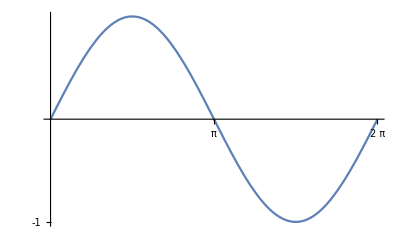

```mathematica
Plot[Sin[x],{x,0,2π},Ticks->{{1π, 2π}, {-1,-0.5-0.5-1}}]
```

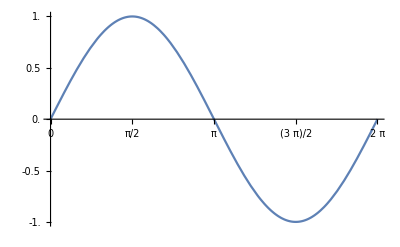

```mathematica
Plot[Sin[x],{x,0,2π},Ticks->{Range[0,2π,π/4],Range[-1,1,0.25]}]
```

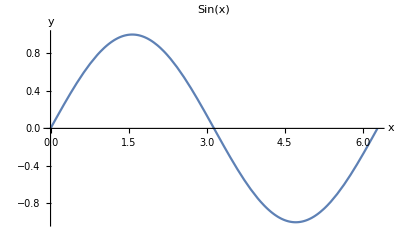

```mathematica
(* PlotLabel与AxesLabel *)
Plot[Sin[x],{x,0,2π},AxesLabel->{"x","y"},PlotLabel->"Sin(x)"]
```

```mathematica
Plot[
Sin[x],
{x,0,2π},
AxesLabel->{
Style[
"x",
FontSize->14,Bold],
Style[
"y",
FontSize->14,Bold]},
PlotLabel->
Style[
"Sin(x)",
FontSize->14,
FontFamily->"Arial",
FontColor->Blue]
]
```

-Graphics-

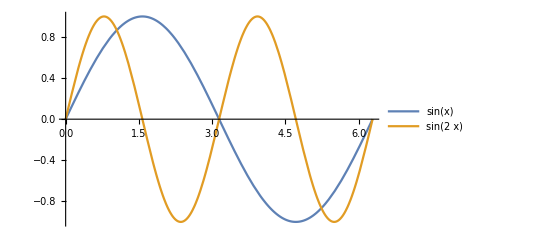

```mathematica
(* PlotLegend *)
Plot[{Sin[x],Sin[2x]},{x,0,2π},PlotLegends->"Expressions"]
```

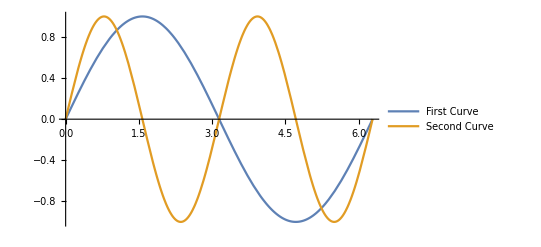

```mathematica
Plot[{Sin[x],Sin[2x]},{x,0,2π},PlotLegends->{"First Curve","Second Curve"}]
```

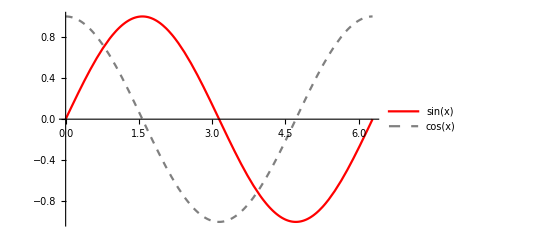

```mathematica
Plot[
	{Sin[x],Cos[x]},
	{x,0,2π},
	PlotStyle->{
		Directive[Red,Thick],
		Directive[Gray,Thick,Dashed]
	},
        PlotLegends->"Expressions"
]
```

```mathematica
(* 调整图例的位置 *)
Plot[{Sin[x],Cos[x]},{x,0,2π},PlotStyle->{Directive[Red,Thick],Directive[Gray,Thick,Dashed]},PlotLegends->Placed["Expressions",Top]]
```

-Graphics-

```mathematica
(* 基于CallOut对图例的位置进行调整 *)
Plot[{Callout[Sin[x],"Sin(x)"],Callout[Cos[x],"Cos(x)"]},{x,0,2π},PlotStyle->{Directive[Red,Thick],Directive[Grey,Dashed]}](* 标注不是图例 *)
```

-Graphics-

```mathematica
Plot[{Callout[Sin[x],"sin(x)",Bottom],Callout[Cos[x],"cos(x)",Bottom]},{x,0,2π},PlotStyle->{Directive[Red,Thick],Directive[Gray,Dashed]}]
```

-Graphics-

```mathematica
Plot[Callout[Tan[x],"tan(x)",2.5],{x,0,2π}]
```

-Graphics-

```mathematica
Plot[Callout[Tan[x],"tan(x)",π],{x,0,2π}]
```

-Graphics-

```mathematica
(* Epilog渲染一个点 *)
Plot[Callout[Tan[x],"tan(x)",π],{x,0,2π},Epilog->{PointSize[Large],Point[{π,0}]}]
```

-Graphics-

```mathematica
Plot3D[Sin[x y],{x,0,π},{y,0,π},Mesh->None]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[u],Sin[u]+Cos[v],Sin[v]},{u,0,2π},{v,-π,π},PlotStyle->Opacity[0.3],Mesh->None]
```

-Graphics3D-

```mathematica
(* 纹理映射 *)
SphericalPlot3D[1+Sin[5x]Sin[10y]/10,{x,0,π},{y,0,2π}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[1+Sin[5x]Sin[10y]/10,{x,0,π},{y,0,2π},Axes->False,Mesh->None,Boxed->False,Background->Black,Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
SphericalPlot3D[1+Sin[5x]Sin[10y]/10,{x,0,π},{y,0,2π},Axes->False,Mesh->None,Boxed->False,Background->Black,Lighting->"Neutral",PlotStyle->{Texture[ExampleData["Texture","Bark"]]}]
```

-Graphics3D-

```mathematica
ExampleData["Texture"]
```

{{Texture,Bark},{Texture,Bark2},{Texture,Bark3},{Texture,Bricks},{Texture,Bricks2},{Texture,Bricks3},{Texture,Bricks4},{Texture,Bricks5},{Texture,Bricks6},{Texture,Bricks7},{Texture,Bricks8},{Texture,BrickWall},{Texture,Bubbles},{Texture,Bubbles2},{Texture,Bubbles3},{Texture,Cloth},{Texture,Cloth2},{Texture,Cloth3},{Texture,Grass},{Texture,Grass2},{Texture,Grass3},{Texture,Grass4},{Texture,Grass5},{Texture,Gravel},{Texture,Herringbone},{Texture,Herringbone2},{Texture,Herringbone3},{Texture,HexagonalHoles},{Texture,Leather},{Texture,Leather2},{Texture,Leather3},{Texture,MetalGrates},{Texture,Mosaic},{Texture,Mosaic2},{Texture,Mosaic3},{Texture,Mosaic4},{Texture,Mosaic5},{Texture,Mosaic6},{Texture,Pigskin},{Texture,Pigskin2},{Texture,Pigskin3},{Texture,Raffia},{Texture,Raffia2},{Texture,Raffia3},{Texture,Sand},{Texture,Sand2},{Texture,Sand3},{Texture,Sand4},{Texture,Sand5},{Texture,Sand6},{Texture,Shingles},{Texture,Shingles2},{Texture,Straw},{Texture,Straw2},{Texture,Straw3},{Texture,TileRoof},{Texture,Wall},{Texture,Water},{Texture,Water2},{Texture,Water3},{Texture,Wood},{Texture,Wood2},{Texture,Wood3},{Texture,WoodFence}}

```mathematica
ExampleData[{"Texture","Bark"}]
```

-Graphics-

```mathematica
(* 定义函数使用plot选项 *)
myPlot[eq1_,eq2_] := Plot[{eq1,eq2},{x,0,2π},PlotStyle->{Directive[Red,Thick],Directive[Gray,Thick,Dashed]},PlotLegends->Placed["Expressions",Above]]
```

```mathematica
myPlot[Sin[x],Cos[x]]
```

-Graphics-

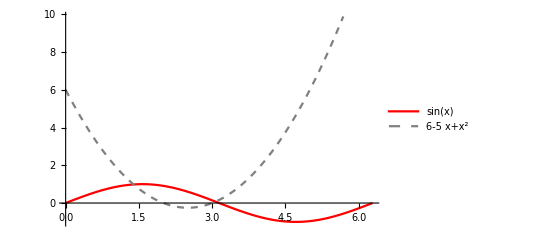

```mathematica
myPlot[Sin[x],6-5x+x^2]
```

```mathematica
mySettings =PlotStyle->{Directive[Red,Thick],Directive[Gray,Thick,Dashed]};
```

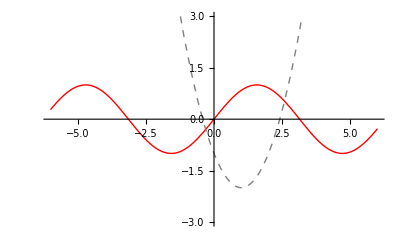

```mathematica
Plot[{Sin[x],x^2-2x-1},{x,-6,6},PlotRange->3,Evaluate[mySettings]]
```

```mathematica
Clear[myPlot,mySettings]
```